```mathematica
arr = {{"1.in",1000,1498,100,130807,139422,119828,155224,170843,175077,216664},{"2.in",2000,5997,100,286412,410125,358180,423060,465281,507215,578263},{"3.in",3000,13495,100,547550,754107,652702,745419,852800,946868,1050186},{"4.in",4000,23994,100,926941,1211463,1074200,1157863,1300364,1440709,1563654},{"5.in",5000,37492,100,1396933,1711335,1524733,1613863,1872341,2013884,2265049},{"6.in",6000,53991,100,1872121,2371444,2103912,2196345,2456903,2708994,3081724},{"7.in",7000,73489,100,2367723,3072536,2799150,2767827,3108936,3522364,3991726},{"8.in",8000,95988,100,3071965,3744596,3610745,3453003,3938856,4244514,4787503},{"9.in",9000,121486,100,4044960,4947974,4359623,4196810,4932372,5291160,6090963},{"10.in",10000,149985,100,5042072,5844175,5349604,5308099,5854461,6454922,7078555},{"11.in",11000,181483,100,5930563,7091762,6416875,6361654,6942255,7434819,8336809},{"12.in",12000,215982,100,7183849,8117224,7614352,7478594,8223572,8973489,9790518},{"13.in",13000,253480,100,8401633,9344211,9197468,8753806,9390633,10102105,11515325},{"14.in",14000,293979,100,9473338,10822818,10450554,9945526,10963068,11660473,13347788},{"15.in",15000,337477,100,11002201,12318294,11760496,11115483,11932858,13012573,14871208},{"16.in",16000,383976,100,12329297,13652624,13162366,12333179,13470104,14618551,16676832},{"17.in",17000,433474,100,13739618,15212922,14634644,13777646,14998211,16114325,18475611},{"18.in",18000,485973,100,15191876,16920207,15985300,15362695,16339431,17667224,21034548},{"19.in",19000,541471,100,16777459,18388790,17704809,16777011,17895991,19196134,22944611},{"20.in",20000,599970,100,18066615,19968050,18979814,18080229,20111905,20759659,26172125}
};
```

```mathematica
list = Array[{arr[[#1,3]],arr[[#1,#2+4]]}&,{Length[arr],7}]
```

{{{1000,130807},{1000,139422},{1000,119828},{1000,155224},{1000,170843},{1000,175077},{1000,216664}},{{2000,286412},{2000,410125},{2000,358180},{2000,423060},{2000,465281},{2000,507215},{2000,578263}},{{3000,547550},{3000,754107},{3000,652702},{3000,745419},{3000,852800},{3000,946868},{3000,1050186}},{{4000,926941},{4000,1211463},{4000,1074200},{4000,1157863},{4000,1300364},{4000,1440709},{4000,1563654}},{{5000,1396933},{5000,1711335},{5000,1524733},{5000,1613863},{5000,1872341},{5000,2013884},{5000,2265049}},{{6000,1872121},{6000,2371444},{6000,2103912},{6000,2196345},{6000,2456903},{6000,2708994},{6000,3081724}},{{7000,2367723},{7000,3072536},{7000,2799150},{7000,2767827},{7000,3108936},{7000,3522364},{7000,3991726}},{{8000,3071965},{8000,3744596},{8000,3610745},{8000,3453003},{8000,3938856},{8000,4244514},{8000,4787503}},{{9000,4044960},{9000,4947974},{9000,4359623},{9000,4196810},{9000,4932372},{9000,5291160},{9000,6090963}},{{10000,5042072},{10000,5844175},{10000,5349604},{10000,5308099},{10000,5854461},{10000,6454922},{10000,7078555}},{{11000,5930563},{11000,7091762},{11000,6416875},{11000,6361654},{11000,6942255},{11000,7434819},{11000,8336809}},{{12000,7183849},{12000,8117224},{12000,7614352},{12000,7478594},{12000,8223572},{12000,8973489},{12000,9790518}},{{13000,8401633},{13000,9344211},{13000,9197468},{13000,8753806},{13000,9390633},{13000,10102105},{13000,11515325}},{{14000,9473338},{14000,10822818},{14000,10450554},{14000,9945526},{14000,10963068},{14000,11660473},{14000,13347788}},{{15000,11002201},{15000,12318294},{15000,11760496},{15000,11115483},{15000,11932858},{15000,13012573},{15000,14871208}},{{16000,12329297},{16000,13652624},{16000,13162366},{16000,12333179},{16000,13470104},{16000,14618551},{16000,16676832}},{{17000,13739618},{17000,15212922},{17000,14634644},{17000,13777646},{17000,14998211},{17000,16114325},{17000,18475611}},{{18000,15191876},{18000,16920207},{18000,15985300},{18000,15362695},{18000,16339431},{18000,17667224},{18000,21034548}},{{19000,16777459},{19000,18388790},{19000,17704809},{19000,16777011},{19000,17895991},{19000,19196134},{19000,22944611}},{{20000,18066615},{20000,19968050},{20000,18979814},{20000,18080229},{20000,20111905},{20000,20759659},{20000,26172125}}}

```mathematica
mat = Transpose[list]
```

{{{1000,130807},{2000,286412},{3000,547550},{4000,926941},{5000,1396933},{6000,1872121},{7000,2367723},{8000,3071965},{9000,4044960},{10000,5042072},{11000,5930563},{12000,7183849},{13000,8401633},{14000,9473338},{15000,11002201},{16000,12329297},{17000,13739618},{18000,15191876},{19000,16777459},{20000,18066615}},{{1000,139422},{2000,410125},{3000,754107},{4000,1211463},{5000,1711335},{6000,2371444},{7000,3072536},{8000,3744596},{9000,4947974},{10000,5844175},{11000,7091762},{12000,8117224},{13000,9344211},{14000,10822818},{15000,12318294},{16000,13652624},{17000,15212922},{18000,16920207},{19000,18388790},{20000,19968050}},{{1000,119828},{2000,358180},{3000,652702},{4000,1074200},{5000,1524733},{6000,2103912},{7000,2799150},{8000,3610745},{9000,4359623},{10000,5349604},{11000,6416875},{12000,7614352},{13000,9197468},{14000,10450554},{15000,11760496},{16000,13162366},{17000,14634644},{18000,15985300},{19000,17704809},{20000,18979814}},{{1000,155224},{2000,423060},{3000,745419},{4000,1157863},{5000,1613863},{6000,2196345},{7000,2767827},{8000,3453003},{9000,4196810},{10000,5308099},{11000,6361654},{12000,7478594},{13000,8753806},{14000,9945526},{15000,11115483},{16000,12333179},{17000,13777646},{18000,15362695},{19000,16777011},{20000,18080229}},{{1000,170843},{2000,465281},{3000,852800},{4000,1300364},{5000,1872341},{6000,2456903},{7000,3108936},{8000,3938856},{9000,4932372},{10000,5854461},{11000,6942255},{12000,8223572},{13000,9390633},{14000,10963068},{15000,11932858},{16000,13470104},{17000,14998211},{18000,16339431},{19000,17895991},{20000,20111905}},{{1000,175077},{2000,507215},{3000,946868},{4000,1440709},{5000,2013884},{6000,2708994},{7000,3522364},{8000,4244514},{9000,5291160},{10000,6454922},{11000,7434819},{12000,8973489},{13000,10102105},{14000,11660473},{15000,13012573},{16000,14618551},{17000,16114325},{18000,17667224},{19000,19196134},{20000,20759659}},{{1000,216664},{2000,578263},{3000,1050186},{4000,1563654},{5000,2265049},{6000,3081724},{7000,3991726},{8000,4787503},{9000,6090963},{10000,7078555},{11000,8336809},{12000,9790518},{13000,11515325},{14000,13347788},{15000,14871208},{16000,16676832},{17000,18475611},{18000,21034548},{19000,22944611},{20000,26172125}}}

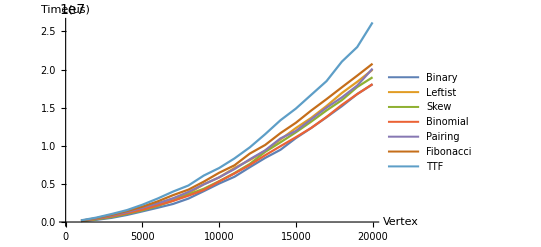

```mathematica
names = {"Binary","Leftist","Skew","Binomial","Pairing","Fibonacci","TTF"};
plots = ListLinePlot[Array[Legended[mat[[#]],names[[#]]]&,7],PlotStyle->Thickness[0.004],AxesLabel->{"Edge","Time(us)"}]
```